# FormCalc: top-quark pair production (parton level)

## gluon-gluon initial state

```mathematica
Exit[];
```

### Set Up

```mathematica
$Language="English";
<<FeynArts`
<<FormCalc`
```

FeynArts 3.11 (3 Aug 2020)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.9 (28 Aug 2020)

by Thomas Hahn

### Topology

> Top. 1 aebe/cede/0.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebf/cedf/ef.m, 0 diagrams

> Top. 4 aebf/cfde/ef.m, 0 diagrams



FeynArtsGraphics[2→2][([T1] | [T2] | [T3]
[T4] | Null | Null
Null | Null | Null)]

```mathematica
topologies=CreateTopologies[0,2->2];
Paint[topologies]
```

### Diagram

```mathematica
InitializeModel["dim_6_c6_c8c", GenericModel -> "dim_6_c6_c8c"];
```

loading generic model file /Users/jaco/Documents/PhD/CAPP21/Thomas Hahn Lecture 4/FormCalc/FeynArts-3.11/Models/dim_6_c6_c8c.gen

> $GenericMixing is OFF

generic model {dim_6_c6_c8c} initialized

loading classes model file /Users/jaco/Documents/PhD/CAPP21/Thomas Hahn Lecture 4/FormCalc/FeynArts-3.11/Models/dim_6_c6_c8c.mod

> 49 particles (incl. antiparticles) in 22 classes

> $CounterTerms are ON

> 124 vertices

classes model {dim_6_c6_c8c} initialized

Excluding 0 Generic, 3 Classes, and 3 Particles fields

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

> Top. 2: 1 Classes insertion

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

Restoring 0 Generic, 3 Classes, and 3 Particles fields

in total: 4 Classes insertions

> Top. 1 aebe/cede/0.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebf/cedf/ef.m, 0 diagrams

> Top. 4 aebf/cfde/ef.m, 0 diagrams

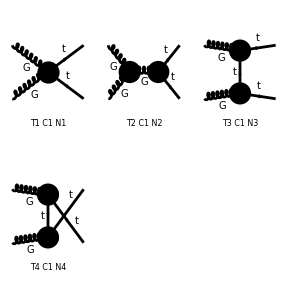

```mathematica
diagrams=InsertFields[topologies,
{V[4], V[4]}->{F[30], -F[30]},InsertionLevel->{Classes},
Model->"dim_6_c6_c8c", GenericModel-> "dim_6_c6_c8c", ExcludeParticles-> {V[1],V[2],S[1]}
];

Paint[diagrams];
```

### Amplitude

```mathematica
ClearProcess[];
amplitude=CalcFeynAmp[CreateFeynAmp[diagrams], FermionChains->VA];
squared=SquaredME[amplitude];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

> Top. 4: 1 Classes amplitude

in total: 4 Classes amplitudes

preparing FORM code in /Users/jaco/fc-amp-1.frm

running FORM...

ok

### Helicities

```mathematica
(*Only for fermions*)
_Hel=0;
squared=squared//.HelicityME[amplitude];
```

> 144 helicity matrix elements

preparing FORM code in /Users/jaco/fc-hel-5.frm

running FORM...

ok

### Colour

```mathematica
squared = ExpandSums[squared//.ColourME[amplitude]];
```

### Polarizations

```mathematica
rawResult = PolarizationSum[squared,GaugeTerms->False]//.Join[Subexpr[],Abbr[]];
result=4/(8 * 8)*rawResult; (*Multiply by two for each ougoing fermion, divide by the colour factor (8 for gluons, 3 for quarks) and by initial vector particles*)
```

preparing FORM code in /Users/jaco/fc-pol-13.frm

running FORM...

ok

### Replacements

```mathematica
repl = {vevhat-> v, LambdaSMEFT-> Λ, MU-> 0, MU2-> 0, MD-> 0, MD2-> 0};
```

```mathematica
MyResult = result//.Join[Abbr[],Subexpr[], M$FACouplings,{Den[p2_,m2_]:>1/(p2-m2)},repl ];
```

```mathematica
MyResultSimplified=Simplify[MyResult, Assumptions->{Element[Λ , Reals], Element[v, Reals], Element[ctGRe, Reals], Element[cuGRe, Reals], Element[cuGIm, Reals], Element[ctGIm, Reals]}];
```

```mathematica
dim6Sq = Collect[MyResultSimplified//Expand, 1/Λ^2];
dim6Sm = dim6Sq/.{Λ^b_/;b≠0->0};
dim6Quad = (dim6Sq - dim6Sm)/.{Λ^b_/;b≠-4->0} ;
dim6Lin =(dim6Sq -  dim6Sm)/.{Λ^b_/;b≠-2->0} ;
```

```mathematica
dim6Sm = dim6Sm//FullSimplify
```

-1/(3 S^2 (MT2-T)^2 (MT2-U)^2)2 Alfas2 π^2 (-36 MT2^5 T-MT2 (S T (15 S^3-35 S^2 T-84 S T^2+14 T^3)+(-S^4+27 S^3 T-126 S^2 T^2+99 S T^3+72 T^4) U+(30 S^3+184 S^2 T+119 S T^2+72 T^3) U^2+S (51 S+292 T) U^3+36 (S+T) U^4)+2 MT2^4 (7 S^2+S (-31 T+101 U)+9 (6 T^2+3 T U+U^2))+MT2^3 (S^2 (230 T-201 U)+S (20 T^2-169 T U-411 U^2)-36 (3 T^3+5 T^2 U+T U^2+U^3))+T (S^4 (8 T-U)+S^3 U (-3 T+14 U)+18 T U^2 (2 T^2-T U+U^2)+S^2 (-8 T^3-20 T^2 U+34 T U^2+35 U^3)+S U (14 T^3+43 T^2 U+47 T U^2+36 U^3))+MT2^2 (7 S^4+S^3 (-51 T+62 U)+S^2 (-240 T^2-81 T U+262 U^2)+S (56 T^3+52 T^2 U+487 T U^2+245 U^3)+18 (2 T^4+11 T^3 U+3 T^2 U^2+3 T U^3+U^4)))

```mathematica
dim6Lin = dim6Lin//.{GS -> √(4π Alfas),  cuGIm-> 0, ctGIm-> 0, cuGRe-> 0}//FullSimplify
```

1/(3 S^2 (MT2-T)^2 (MT2-U)^2 Λ^2)√2 Alfas^(3/2) ctGRe MT π^(3/2) (288 MT2^6+12 MT2^5 (79 S-84 T-72 U)+72 T^2 U^2 (T+U) (2 T+U)+S^4 (64 T^2+15 T U+32 U^2)+2 S T U (4 T^3+175 T^2 U+143 T U^2+8 U^3)+2 S^3 (8 T^3+2 T^2 U+85 T U^2+20 U^3)+S^2 (-48 T^4-179 T^3 U+262 T^2 U^2+83 T U^3+8 U^4)+2 MT2^4 (-734 S^2-9 S (119 T+55 U)+36 (18 T^2+39 T U+13 U^2))+MT2^3 (183 S^3+S^2 (2971 T+1307 U)+2 S (751 T^2+876 T U-103 U^2)-144 (5 T^3+23 T^2 U+19 T U^2+3 U^3))+MT2^2 (111 S^4+S^3 (-267 T+131 U)-2 S^2 (1157 T^2+718 T U+138 U^2)+12 S (-25 T^3-60 T^2 U+77 T U^2+22 U^3)+72 (2 T^4+23 T^3 U+39 T^2 U^2+15 T U^3+U^4))+MT2 (S^3 (T-2 U) (236 T+41 U)-S^4 (143 T+79 U)-144 T U (2 T^3+8 T^2 U+6 T U^2+U^3)+S^2 (659 T^3+900 T^2 U-562 T U^2+93 U^3)-2 S (4 T^4+25 T^3 U+534 T^2 U^2+275 T U^3+8 U^4))) v

```mathematica
dim6Quad = dim6Quad//.{GS -> √(4π Alfas), cuGIm-> 0, ctGIm-> 0, cuGRe-> 0}//FullSimplify
```

-1/(3 S^2 (MT2-T)^2 (MT2-U)^2 Λ^4)Alfas ctGRe^2 π (864 MT2^7+4 MT2^6 (89 S-612 T-576 U)+MT2^5 (-1440 S^2+S (-778 T+392 U)+72 (34 T^2+87 T U+29 U^2))-MT2^4 (173 S^3+S^2 (-3033 T+76 U)+S (-374 T^2+867 T U+1469 U^2)+144 (7 T^3+41 T^2 U+37 T U^2+5 U^3))+S T U (4 S^4+S^3 (3 T+28 U)+S^2 (-59 T^2+40 T U-11 U^2)+S (-64 T^3+46 T^2 U+76 T U^2-71 U^3)-(T+U) (6 T^3-31 T^2 U-38 T U^2+36 U^3))+MT2^3 (280 S^4+S^3 (231 T+1297 U)+S^2 (-2530 T^2+1161 T U+1151 U^2)+S (163 T^3+824 T^2 U+2643 T U^2+958 U^3)+72 (2 T^4+31 T^3 U+63 T^2 U^2+23 T U^3+U^4))+MT2^2 (4 S^5-S^4 (309 T+220 U)-S^3 (37 T^2+1819 T U+711 U^2)+S^2 (617 T^3-494 T^2 U-2201 T U^2-610 U^3)-144 T U (2 T^3+10 T^2 U+8 T U^2+U^3)-S (121 T^4+439 T^3 U+1406 T^2 U^2+1233 T U^3+273 U^4))+MT2 (-4 S^5 (T+U)+72 T^2 U^2 (T+U) (2 T+U)+S^4 (157 T^2-39 T U+100 U^2)+S^3 (163 T^3+437 T^2 U+407 T U^2+235 U^3)+S^2 (8 T^4+313 T^3 U+356 T^2 U^2+558 T U^3+167 U^4)+S (6 T^5+96 T^4 U+207 T^3 U^2+206 T^2 U^3+271 T U^4+36 U^5))) v^2

### Cross section

```mathematica
Clear[pf, pi]
```

```mathematica
pf = pf/.Solve[{√S== √(MT2 +pf^2) + √(MT2 +pf^2)}, pf][[2]]
```

1/2 √(-4 MT2+S)

```mathematica
pi = (pi/.Solve[S ==(√(pi^2)+√(pi^2))^2, pi])[[2]];
```

```mathematica
prefacdOmega = 1/(64 π^2 S)*pf/pi
```

(√(-4 MT2+S))/(64 π^2 S^(3/2))

```mathematica
integraldOmega={dim6Sm, dim6Lin, dim6Quad}//.{T->MT2+MT2-S-U, U-> MT2-2pi*(√(MT2+pf^2)-pf Cos[θ])};
diffXSectiondtheta=2π * prefacdOmega*integraldOmega * Sin[θ];
```

```mathematica
sigma = Integrate[diffXSectiondtheta, {θ, 0, π}, Assumptions->{Element[S, Reals],S>4MT2, MT2>0}]
```

{(Alfas2 π (-√(S (-4 MT2+S)) (31 MT2+7 S)+8 (MT2^2+4 MT2 S+S^2) ArcTanh[√(1-(4 MT2)/S)]))/(3 S^3),-(ctGRe MT √(2 π) (Alfas/S)^(3/2) √(-4 MT2+S) v (-9+16 √(S/(-4 MT2+S)) ArcTanh[√(1-(4 MT2)/S)]))/(3 Λ^2),(Alfas ctGRe^2 v^2 (√(S (-4 MT2+S)) (-18 MT2+7 S)+34 MT2 S ArcTanh[√(1-(4 MT2)/S)]))/(6 S^2 Λ^4)}